# TMD evolution, Cagliari 6/2022 author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/Cagliari22

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site Bastami:2018xqd for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

Contains the following constants:

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
?wwsidis`*
```

## Constants

```mathematica
Mproton = 0.93827;
Mp = Mproton;
Mpion = 0.13957;

Q2compass= 28.;



Λ = 0.2;
CF = 4/3;
CA=3;
TR = 0.5;
TF = 0.5;
Nf = 3;
beta0 = (33 - 2 Nf)/(12 π);
Q0 = 1.3;  (* Starting scale for evolution. *)

MZ = 91.19;


bmax = 1; (* bmax=1 *)



g0 = 0.84;



bstar[bt_] := bt/ Sqrt[1 + bt^2 / bmax^2]; (* b* *)


C1 = 2 Exp[-N[EulerGamma]];   
mub[bt_] := C1 / bstar[bt]; (* mub *)
```

Here we plot b* that is used in the prescription

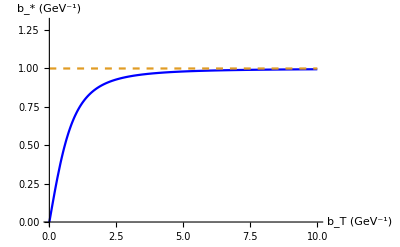

```mathematica
Plot[{bstar[bt],bmax},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","b_* (GeV^-1)"},PlotRange->{0,1.3},PlotStyle->{Blue,Dashed,Red}]
```

Let us also plot μ_b

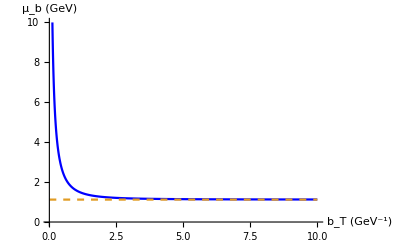

```mathematica
Plot[{mub[bt],C1/bmax,mub[bt,C1]},{bt,0,10},AxesLabel->{"b_T (GeV^-1)","μ_b (GeV)"},PlotRange->{0,10},PlotStyle->{Blue,Dashed}]
```

## QCD strong coupling, alpha s

#### Let us start by constructing a 2 loop solution compatible with CTEQ parametrization

```mathematica
Lambda[Q_]:=Piecewise[{{0.372205,Q≤1.3},{0.325603,1.3≤Q<4.5},{0.2259965,4.5≤Q}}];
NF[Q_]:=Piecewise[{{3,Q≤1.3},{4,1.3≤Q<4.5},{5,4.5≤Q}}];
β[Q_]:=11-2/3 NF[Q];
β1[Q_]:=51-19/3 NF[Q];

AlphaStrong[Q_]:=
(4π)/(β[Q]Log[Q^2/Lambda[Q]^2])(1-(2β1[Q])/β[Q]^2 Log[Log[Q^2/Lambda[Q]^2]]/Log[Q^2/Lambda[Q]^2])
```

```mathematica
AlphaStrong[MZ]
```

0.117981

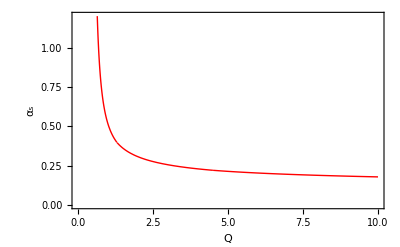

```mathematica
Plot[AlphaStrong[Q],{Q,0.5,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,1.2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q","α_s"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

## Perturbative evolution

One loop result using one loop alpha_s and expansion of gammaF and gammaK

-Graphics-

-Graphics-

-Graphics-

See PhysRevD .96 .054011 for values of perturbative expansion.

```mathematica
gammaK1[mu_] := 8 CF;
gammaK2[mu_]:=CF CA (536/9-(8 π^2)/3)-80/9 CF Nf;

gammaF1[mu_]:=6CF;

gammaK[mu_] := AlphaStrong[mu]/(4π) gammaK1[mu] +(AlphaStrong[mu]/(4 π))^2 gammaK2[mu];
gammaF[mu_] := AlphaStrong[mu]/(4π) gammaF1[mu];

Spert[Q_,Q0_]:= NIntegrate[1/mu (gammaF[mu]-gammaK[mu] Log[Q/mu]),{mu,Q0,Q},Method->"GaussKronrodRule",MaxRecursion->20] //Quiet;
```

```mathematica
Spert[Sqrt[Q2compass],Q0]
```

-0.0682874

Notice Sperp becomes negative.

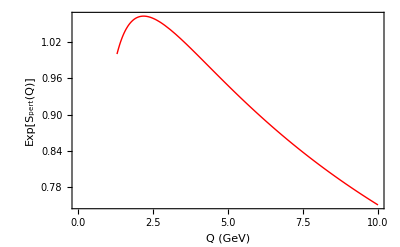

```mathematica
Plot[Exp[Spert[Q,Q0]],{Q,Q0,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"Q (GeV)","Exp[S_pert(Q)]"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

## Collins-Soper evolution kernel K̃ , it gives the Q-dependent change in the distribution, a very characteristic effect of the gluon emissions

One loop solution:

-Graphics-

```mathematica
KtildePert[b_,Q_]:= -8 CF AlphaStrong[Q]/(4 π)Log[(b Q)/(2 Exp[-N[EulerGamma]])]
```

```mathematica
Plot3D[KtildePert[b,Q],{b,0,1},{Q,Q0,10}]
```

-Graphics3D-

It looks like this at the initial scale Q0:

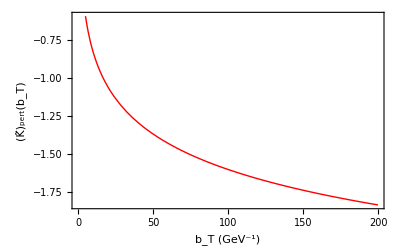

```mathematica
Plot[KtildePert[b,Q0],{b,0,200},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","(K̃)_pert(b_T)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"]]
```

gK from my paper with Kang and Yan

```mathematica
gK[b_] := g0 Log[b/bstar[b]];
```

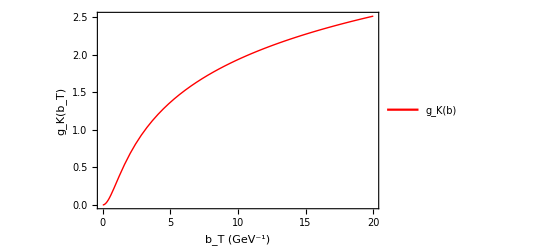

```mathematica
Plot[{gK[b]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Cyan,Dotted}}, FrameLabel->{"b_T (GeV^-1)","g_K(b_T)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"g_K(b)" },{0.7,0.7}]]
```

-Graphics-

See https : // mathematica.stackexchange.com/questions/10533/nested - nintegrate for explanation of ?NumericQ

```mathematica
RGrunningKtilde[b_?NumericQ,Q0_?NumericQ]:=NIntegrate[1/mu gammaK1[mu] ,{mu,mub[b],Q0},PrecisionGoal->2,AccuracyGoal->2] //Quiet;
```

```mathematica
Ktilde[b_?NumericQ,Q0_?NumericQ]:= KtildePert[bstar[b],mub[b]]- RGrunningKtilde[b,Q0]- gK[b];
```

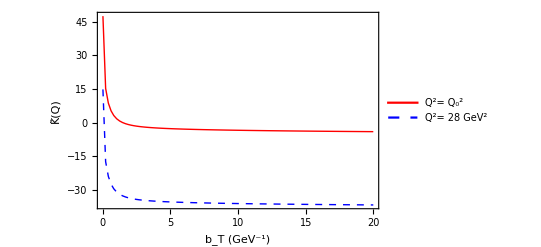

```mathematica
Plot[{Ktilde[b,Q0],Ktilde[b,Q2compass]},{b,0.01,20},PlotRange->{{0,20},Automatic},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","K̃(Q)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"Q^2= Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2"},{0.7,0.7}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

## Definition of Evolution factor and Hard factor to be used in estimates

-Graphics-

```mathematica
EvolutionFactor[b_?NumericQ,Q2_?NumericQ]:= Exp[1/2(KtildePert[b,mub[b]] -gK[b])Log[Q2/Q0^2]]Exp[Spert[Sqrt[Q2],Q0]];
```

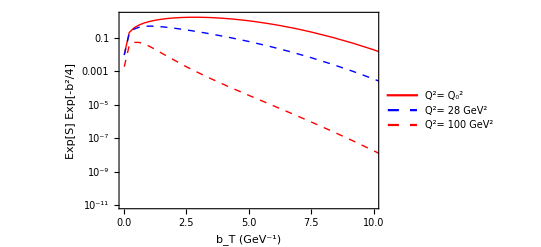

```mathematica
avk = 0.25;
LogPlot[{b Exp[-(b^2 avk)/4] EvolutionFactor[b,Q0^2], b Exp[-(b^2 avk)/4] EvolutionFactor[b,Q2compass],b Exp[-(b^2 avk)/4]EvolutionFactor[b,100.*100.]},{b,0.01,20},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{10^(-11),2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","Exp[S] Exp[-b^2/4]"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"Q^2= Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2"},{0.7,0.7}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

## Evolution for f_1 and f_(1T)^⊥, may be slow to run!

## Evo Fourier Transforms kT ⇔ bT parton distributions

```mathematica
(* 0 moment in TMD gaussian approximation *)
fb0[b_]:=f0 Exp[-(b^2 av)/4];
(* 0 moment in TMD gaussian approximation *)
fk0[kt_]:=f0 1/(π av)Exp[-kt^2/av];
(* 1 moment in TMD gaussian approximation *)
fb1[b_]:=f1 Exp[-(b^2 av)/4];
(* 1 moment in TMD gaussian approximation *)
fk1[kt_]:=f1(2 M^2)/(π av^2)Exp[-kt^2/av];
(* 2 moment in TMD gaussian approximation *)
fb2[b_]:=f2 Exp[-(b^2 av)/4];
(* 2 moment in TMD gaussian approximation *)
fk2[kt_]:=f2(2 M^4)/(π av^3)Exp[-kt^2/av];
```

kT ⟹ bT transforms

```mathematica
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},2 π Integrate[kt BesselJ[0,kt b] fk0[kt],{kt,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},(2 π)/M^2 Integrate[kt BesselJ[1,kt b] kt/b fk1[kt],{kt,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},(2 π 2)/M^4 Integrate[kt BesselJ[2,kt b] (kt/b)^2 fk2[kt],{kt,0,Infinity}]]
```

ⅇ^(-(av b^2)/4) f0

ⅇ^(-(av b^2)/4) f1

ⅇ^(-(av b^2)/4) f2

bT ⟹ kT transforms

```mathematica
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},1/(2 π) Integrate[b BesselJ[0,kt b]fb0[b],{b,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},M^2/(2 π)Integrate[b BesselJ[1,kt b] b/kt fb1[b],{b,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{b>0,kt>0,av>0,M>0},M^4/(2 π 2)Integrate[b BesselJ[2,kt b] (b/kt)^2 fb2[b],{b,0,Infinity}]]
```

(ⅇ^(-kt^2/av) f0)/(av π)

(2 ⅇ^(-kt^2/av) f1 M^2)/(av^2 π)

(2 ⅇ^(-kt^2/av) f2 M^4)/(av^3 π)

```mathematica
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{kt>0,av>0},2 π  Integrate[kt  fk0[kt],{kt,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{kt>0,av>0}, 2 π Integrate[kt  kt^2/(2 M^2) fk1[kt],{kt,0,Infinity}]]
(* Explicit calculations using (2.16) from Boer 2011 *)
Assuming[{kt>0,av>0},2 π Integrate[kt  (kt^2/(2 M^2))^2 fk2[kt],{kt,0,Infinity}]]
```

f0

f1

f2

## Evo f_1

```mathematica
(*2005 fit Appendix A.1 [hep-ph/0501196]*)
avk=0.25;
(* distribution*)


f1ub[x_,b_,Q2_ ]:=f1u[x,Q2]  Exp[-(b^2 avk)/4]Sqrt[EvolutionFactor[b,Q2]];
f1uNaiveb[x_,b_,Q2_ ]:= f1u[x,Q2]   Exp[-(b^2 avk)/4];
f1u[x_?NumericQ,kT_?NumericQ,Q2_ ?NumericQ]:= NIntegrate[b/(2 π) BesselJ[0,kT b] f1ub[x,b,Q2 ],{b,0,10},PrecisionGoal->2,AccuracyGoal->2];
(*naive TMD*)
f1uNaive[x_,kT_,Q2_ ]:= f1u[x,Q2] 1/(π avk)  Exp[-kT^2/avk];
```

```mathematica
x1=0.1
```

0.1

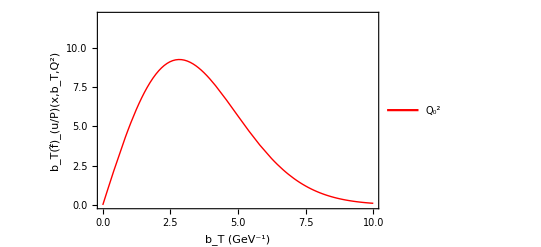

```mathematica
f1plot =Plot[{b f1uNaiveb[x1,b,Q0*Q0 ]},{b,0.,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,12}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","b_T(f̃)_(u/P)(x,b_T,Q^2)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"Q_0^2","u Q2compass","u Q0^2 naive","d̄"},{0.7,0.7}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

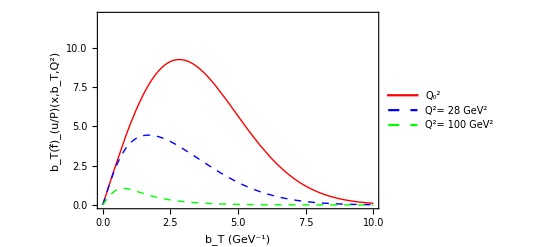

```mathematica
f1plot =Plot[{b f1ub[x1,b,Q0*Q0 ],b f1ub[x1,b,Q2compass ],b f1ub[x1,b,100^2 ]},{b,0.,10},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,10},{0,12}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","b_T(f̃)_(u/P)(x,b_T,Q^2)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2","d̄"},{0.75,0.7}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

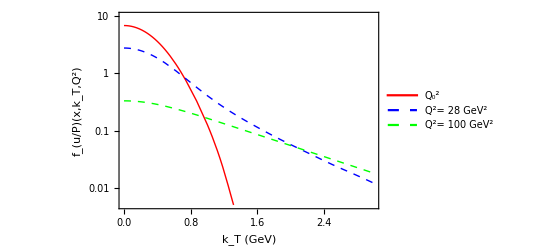

```mathematica
f1plot =LogPlot[{f1u[x1,kt,Q0*Q0 ],f1u[x1,kt,Q2compass ],f1u[x1,kt,100^2 ]},{kt,0.,3},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,3},{5*10^(-3),10^1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Green,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"k_T (GeV)","f_(u/P)(x,k_T,Q^2)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"Q_0^2","Q^2= 28 GeV^2","Q^2= 100 GeV^2","d̄"},{0.7,0.8}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

## Evo f_(1T)^⊥ SIDIS

```mathematica
f1Tperpub[x_?NumericQ,b_?NumericQ,Q2_?NumericQ ]:=f1TperpuFirstMoment[x,Q2]Exp[-(b^2 avks)/4]Sqrt[EvolutionFactor[b,Q2]];
f1Tperpu[x_?NumericQ,kT_?NumericQ,Q2_?NumericQ ]:=Mp^2/(2 π) NIntegrate[b BesselJ[1,kT b] b/kT f1Tperpub[x,b,Q2 ],{b,0,20},PrecisionGoal->2,AccuracyGoal->2];
f1TperpuNaiveb[x_,b_,Q2_]:= f1TperpuFirstMoment[x,Q2]  Exp[-(b^2 avks)/4];
f1TperpuNaive[x_,kT_,Q2_]:= f1TperpuFirstMoment[x,Q2] (2 Mp^2)/(π avks^2) Exp[-kT^2/avks];
```

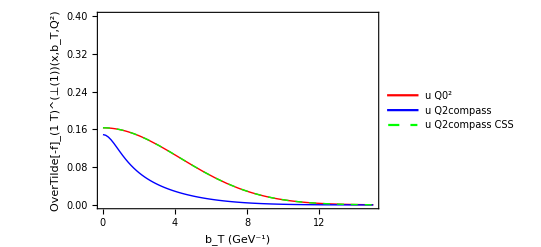

```mathematica
x1 = 0.2;
f1plot =Plot[{-f1Tperpub[x1,b,Q0*Q0 ],-f1Tperpub[x1,b,Q2compass ],-f1TperpuNaiveb[x1,b,Q0*Q0 ]},{b,0.01,15},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,15},{0,0.4}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"b_T (GeV^-1)","OverTilde[-f]_(1  T)^(⊥(1))(x,b_T,Q^2)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u Q0^2","u Q2compass","u Q2compass CSS","u Q0^2"},{0.7,0.7}],PerformanceGoal:>"Speed",MaxRecursion->2]
```

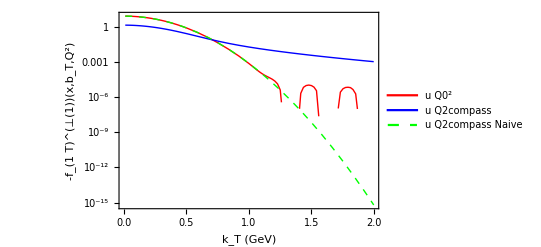

```mathematica
x1 = 0.2;
f1plot =LogPlot[{-f1Tperpu[x1,kt,Q0*Q0 ],-f1Tperpu[x1,kt,Q2compass ],-f1TperpuNaive[x1,kt,Q0*Q0 ]},{kt,0.01,2},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,2},Automatic},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"k_T (GeV)","-f_(1  T)^(⊥(1))(x,b_T,Q^2)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u Q0^2","u Q2compass","u Q2compass Naive"},{0.3,0.2}],PerformanceGoal:>"Speed",MaxRecursion->2]
```